```mathematica
$Assumptions := {mu ∈ Reals && mu > 0 && x<0 && phi ∈ Reals && λ ∈ Reals && A0 ∈ Reals && kz ∈ Reals && ϕ ∈ Reals  && ω ∈ Reals && η ∈ Reals && η >0 && ky ∈ Reals && α ∈ Reals && r ∈ Reals && Tan[α]∈ Reals && Sec[α]∈ Reals};
```

```mathematica
(* Eigenvalue Equation *)
```

```mathematica
Clear[a1,a2,a3]
```

```mathematica
{{-λ,Exp[I phi] kx + a1, Exp[-I phi] ky + a2},{Conjugate[a1]+Exp[-I phi]kx,-λ,Exp[I phi]kz + a3},{Exp[I phi] ky + Conjugate[a2],Exp[-I phi]kz + Conjugate[a3],-λ}}//Det//Simplify
```

λ (a1 ⅇ^(-ⅈ phi) kx+kx^2-λ^2+(a1+ⅇ^(ⅈ phi) kx) Conjugate[a1])+(a3 ⅇ^(ⅈ phi) kx+ⅇ^(2 ⅈ phi) kx kz+a1 (a3+ⅇ^(ⅈ phi) kz)+a2 λ+ⅇ^(-ⅈ phi) ky λ) (ⅇ^(ⅈ phi) ky+Conjugate[a2])+ⅇ^(-3 ⅈ phi) (a2 ⅇ^(ⅈ phi) kx+kx ky+a3 ⅇ^(2 ⅈ phi) λ+ⅇ^(3 ⅈ phi) kz λ+ⅇ^(ⅈ phi) (a2 ⅇ^(ⅈ phi)+ky) Conjugate[a1]) (kz+ⅇ^(ⅈ phi) Conjugate[a3])

```mathematica
Coefficient[%111,λ]/.{α->0,phi->ϕ}//Simplify
```

kx^2+ky^2+kz^2+(A0^4 (-1+η)^2)/(4 ω^2)+(ⅈ A0^2 ⅇ^(-3 ⅈ ϕ) (-1+ⅇ^(6 ⅈ ϕ)) kz (-1+η))/(2 ω)

```mathematica
%278/.{λ->0,phi->ϕ}
```

(a3 ⅇ^(ⅈ ϕ) kx+ⅇ^(2 ⅈ ϕ) kx kz+a1 (a3+ⅇ^(ⅈ ϕ) kz)) (ⅇ^(ⅈ ϕ) ky+Conjugate[a2])+ⅇ^(-3 ⅈ ϕ) (a2 ⅇ^(ⅈ ϕ) kx+kx ky+ⅇ^(ⅈ ϕ) (a2 ⅇ^(ⅈ ϕ)+ky) Conjugate[a1]) (kz+ⅇ^(ⅈ ϕ) Conjugate[a3])

```mathematica
(* Gap Finding *)
```

The eigenvalue equation is,  , in our case we have,

```mathematica
Q[a_,b_] := (a^2-3 b)/9
R[a_,b_,c_]:=( 2 a^3-9a b+27 c)/54
M[a_,b_,c_]:=R[a,b,c]^2-Q[a,b]^3
theata[a_,b_,c_]:= ArcCos[R[a,b,c]/Sqrt[Q[a,b]^3]]
```

```mathematica
Clear[b,c]
```

```mathematica
root1 = -(2 Sqrt[Q[a,b]] Cos [theata[a,b,c]/3])- a/3/.a->0;
```

```mathematica
root2= -(2 Sqrt[Q[a,b]] Cos [(theata[a,b,c]+ 2 Pi)/3])- a/3/.a->0;
```

```mathematica
(* The Gap Equation *)
```

```mathematica
gapsquare = (root1-root2)^2//FullSimplify
```

-4 b Sin[1/3 (π+ArcCos[(3 √3 c)/(2 √(-b^3))])]^2

```mathematica
Clear[a1,a2,a3,b]
```

```mathematica
b = -(Abs[a1]^2+Abs[a2]^2+Abs[a3]^2 + kx(a1 Exp[-I ϕ]+Conjugate[a1]Exp[ I ϕ])+ky(a2 Exp[I ϕ]+Conjugate[a2]Exp[ -I ϕ])+kz(a3 Exp[-I ϕ]+Conjugate[a3]Exp[ I ϕ])+kx^2+ky^2+kz^2);
```

```mathematica
Clear[a1,a2,a3]
```

```mathematica
c =-((a3 ⅇ^(ⅈ ϕ) kx+ⅇ^(2 ⅈ ϕ) kx kz+a1 (a3+ⅇ^(ⅈ ϕ) kz)) (ⅇ^(ⅈ ϕ) ky+Conjugate[a2])+ⅇ^(-3 ⅈ ϕ) (a2 ⅇ^(ⅈ ϕ) kx+kx ky+ⅇ^(ⅈ ϕ) (a2 ⅇ^(ⅈ ϕ)+ky) Conjugate[a1]) (kz+ⅇ^(ⅈ ϕ) Conjugate[a3]))/. phi->ϕ;
```

```mathematica
(* for alpha=0, r = √η *)
```

```mathematica
a1 = I (Exp[-2 I ϕ]kz)/(2 η ω)A0 (η - r Cos[α])/.{α->0,r->Sqrt[η]}
```

(ⅈ A0 ⅇ^(-2 ⅈ ϕ) kz (-√η+η))/(2 η ω)

```mathematica
a2 = I (Exp[2 I ϕ]kz)/(2 η ω) A0 r Sin[α]/.{α->0,r->Sqrt[η]}
```

0

```mathematica
a3 = - I Exp[-2 I ϕ] A0/(2 ω η)( A0 r^2 + (kx - A0)η - r (kx Cos[α] + ky Sin[α]))/.{α->0,r->Sqrt[η],kx->0}
```

0

```mathematica
b/.{kx->0}//FullSimplify
```

-ky^2-kz^2-1/4 Abs[(A0 kz (1-1/(√η)))/ω]^2

```mathematica
c /.{kx->0}//FullSimplify
```

-(ⅈ A0 ky kz^2 (-1+√η))/(√η ω)

```mathematica
gapsquare/.{kx->0}//FullSimplify
```

$Aborted

```mathematica
(* for alpha=π/2, r = √η *)
```

```mathematica
a1 = I (Exp[-2 I ϕ]kz)/(2 η ω)A0 (η - r Cos[α])/.{α->Pi/2,r->Sqrt[η]}
a2 = I (Exp[2 I ϕ]kz)/(2 η ω) A0 r Sin[α]/.{α->Pi/2,r->Sqrt[η]}
a3 = - I Exp[-2 I ϕ] A0/(2 ω η)( A0 r^2 + (kx - A0)η - r (kx Cos[α] + ky Sin[α]))/.{α->Pi/2,r->Sqrt[η],kx->0}
```

(ⅈ A0 ⅇ^(-2 ⅈ ϕ) kz)/(2 ω)

(ⅈ A0 ⅇ^(2 ⅈ ϕ) kz)/(2 √η ω)

(ⅈ A0 ⅇ^(-2 ⅈ ϕ) ky)/(2 √η ω)

```mathematica
b/.{kx->0}//FullSimplify
c/.{kx->0}//FullSimplify
```

-ky^2-kz^2-1/4 Abs[(A0 kz (1-1/(√η)))/ω]^2

-1/(4 η ω^3)ⅈ A0 kz (4 ky kz η ω^2+A0^2 ky kz Cos[6 ϕ]+2 A0 (ky-kz) (ky+kz) √η ω Sin[3 ϕ])

```mathematica
(* r = √η *)
a1 = I (Exp[-2 I ϕ]kz)/(2 η ω)A0 (η - r Cos[α])/.{r->Sqrt[η]}
a2 = I (Exp[2 I ϕ]kz)/(2 η ω) A0 r Sin[α]/.{r->Sqrt[η]}
a3 = - I Exp[-2 I ϕ] A0/(2 ω η)( A0 r^2 + (kx - A0)η - r (kx Cos[α] + ky Sin[α]))/.{r->Sqrt[η],kx->0}
```

(ⅈ A0 ⅇ^(-2 ⅈ ϕ) kz (η-√η Cos[α]))/(2 η ω)

(ⅈ A0 ⅇ^(2 ⅈ ϕ) kz Sin[α])/(2 √η ω)

(ⅈ A0 ⅇ^(-2 ⅈ ϕ) ky Sin[α])/(2 √η ω)

```mathematica
b/.{kx->0}//FullSimplify
```

-ky^2-kz^2-1/4 Abs[(A0 kz (1-1/(√η)))/ω]^2

```mathematica
c/.{kx->0}//FullSimplify
```

-1/(4 η^(3/2) ω^3)ⅈ A0 kz (√η-Cos[α]) (4 ky kz η ω^2+A0 Sin[α] (A0 ky kz Cos[6 ϕ] Sin[α]+2 (ky-kz) (ky+kz) √η ω Sin[3 ϕ]))

```mathematica
(* r = η /Cos[α]*)
```

```mathematica
a1 = I (Exp[-2 I ϕ]kz)/(2 η ω)A0 (η - r Cos[α])/.{r->η /Cos[α]}
a2 = I (Exp[2 I ϕ]kz)/(2 η ω) A0 r Sin[α]/.{r->η /Cos[α]}
a3 = - I Exp[-2 I ϕ] A0/(2 ω η)( A0 r^2 + (kx - A0)η - r (kx Cos[α] + ky Sin[α]))/.{r->η/ Cos[α],kx->0}
```

0

(ⅈ A0 ⅇ^(2 ⅈ ϕ) kz Tan[α])/(2 ω)

-(ⅈ A0 ⅇ^(-2 ⅈ ϕ) (-A0 η+A0 η^2 Sec[α]^2-ky η Tan[α]))/(2 η ω)

```mathematica
b/.{kx->0}//FullSimplify
c/.{kx->0}//Simplify
```

1/(4 ω)ⅇ^(-3 ⅈ ϕ) (2 ⅈ A0^2 kz (-1+η Sec[α]^2)-2 ⅈ A0^2 ⅇ^(6 ⅈ ϕ) kz (-1+η Sec[α]^2)-ⅇ^(3 ⅈ ϕ) ω (4 ky^2+4 kz^2+Abs[(A0 kz Tan[α])/ω]^2+(A0^2 (A0-A0 η Sec[α]^2+ky Tan[α])^2)/ω^2))

0

```mathematica
D[%184,kz]
D[%184,ky]
```

-1/(4 ω)(2 ⅈ A0^2 ⅇ^(-3 ⅈ ϕ)-2 ⅈ A0^2 ⅇ^(3 ⅈ ϕ)+8 kz ω+2 ⅈ A0^2 ⅇ^(-3 ⅈ ϕ) (-1+ⅇ^(6 ⅈ ϕ)) η Sec[α]^2+(2 A0^2 kz Tan[α]^2)/ω)

-(8 ky ω+(2 A0^2 Tan[α] (A0-A0 η Sec[α]^2+ky Tan[α]))/ω)/(4 ω)

```mathematica
rules = {kx->0,kz->(2 A0^2 ω Sin[3ϕ](-1+η Sec[α]^2))/(4 ω^2+A0^2 Tan[α]^2),ky->(A0^3 Tan[α](-1+η Sec[α]^2))/(4 ω^2+A0^2 Tan[α]^2)};
```

```mathematica
(-4 b /.{kx->0})/.(rules)//FullSimplify
```

(A0^4 (1-2 η+Cos[2 α])^2 Cos[3 ϕ]^2 Sec[α]^4)/(4 ω^2+A0^2 Tan[α]^2)

```mathematica
Limit[%239/.{kx->0},α->0]//FullSimplify
```

Limit::alimv: Warning: Assumptions that involve the limit variable are ignored.

(A0^4 (-1+η)^2 Cos[3 ϕ]^2)/ω^2

```mathematica
(* α = Π/2*)
```

```mathematica
a1 = I (Exp[-2 I ϕ]kz)/(2 η ω)A0 (η - r Cos[α])/.{α->Pi/2}
a2 = I (Exp[2 I ϕ]kz)/(2 η ω) A0 r Sin[α]/.{α->Pi/2}
a3 = - I Exp[-2 I ϕ] A0/(2 ω η)( A0 r^2 + (kx - A0)η - r (kx Cos[α] + ky Sin[α]))/.{α->Pi/2,kx->0}
```

(ⅈ A0 ⅇ^(-2 ⅈ ϕ) kz)/(2 ω)

(ⅈ A0 ⅇ^(2 ⅈ ϕ) kz r)/(2 η ω)

-(ⅈ A0 ⅇ^(-2 ⅈ ϕ) (-ky r+A0 r^2-A0 η))/(2 η ω)

```mathematica
b/.{kx->0}//FullSimplify
c/.{kx->0}//FullSimplify
```

-1/(4 η^2 ω^2)(A0^2 (r^2 (kz^2+(ky-A0 r)^2)+2 A0 r (ky-A0 r) η+(A0^2+kz^2) η^2)+4 (ky^2+kz^2) η^2 ω^2+4 A0^2 kz η (-r^2+η) ω Sin[3 ϕ])

1/(2 η^2 ω^3)A0^2 kz Cos[3 ϕ] (η (-r (-ky^2+kz^2+A0 ky r)+A0 ky η) ω+A0 kz r (-ky r+A0 (r^2-η)) Sin[3 ϕ])

```mathematica
c/.{kx->0}//FullSimplify
```

1/(2 η^2 ω^3)A0^2 kz Cos[3 ϕ] (η (-r (-ky^2+kz^2+A0 ky r)+A0 ky η) ω+A0 kz r (-ky r+A0 (r^2-η)) Sin[3 ϕ])

```mathematica
D[%260,kz]
```

-(A0^2 (2 kz r^2+2 kz η^2)+8 kz η^2 ω^2+4 A0^2 η (-r^2+η) ω Sin[3 ϕ])/(4 η^2 ω^2)

```mathematica
D[%260,ky]
```

-(A0^2 (2 r^2 (ky-A0 r)+2 A0 r η)+8 ky η^2 ω^2)/(4 η^2 ω^2)

```mathematica
Solve[{%262==0,%263==0},{kz,ky}]//FullSimplify
```

{{kz→ConditionalExpression[(2 A0^2 (r^2-η) η ω Sin[3 ϕ])/(A0^2 (r^2+η^2)+4 η^2 ω^2), ],ky→ConditionalExpression[(A0^3 r (r^2-η))/(A0^2 r^2+4 η^2 ω^2), ]}}

```mathematica
%260 /.Flatten[%266]//FullSimplify
```

ConditionalExpression[-((A0^4 (r^2-η)^2 (A0^2 (r^2+2 η^2)+4 η^2 ω^2+(A0^2 r^2+4 η^2 ω^2) Cos[6 ϕ]))/(2 (A0^2 r^2+4 η^2 ω^2) (A0^2 (r^2+η^2)+4 η^2 ω^2))), ]

```mathematica
%294 /.Flatten[%266]//FullSimplify
```

ConditionalExpression[-((A0^8 r (r^2-η)^3 η^2 ω (A0^4 (r^4+2 r^2 η^2+2 η^4)+8 A0^2 η^2 (r^2+η^2) ω^2+16 η^4 ω^4+(A0^2 r^2+4 η^2 ω^2) (A0^2 (r^2+2 η^2)+4 η^2 ω^2) Cos[6 ϕ]) Sin[6 ϕ])/((A0^2 r^2+4 η^2 ω^2)^2 (A0^2 (r^2+η^2)+4 η^2 ω^2)^3)), ]

```mathematica
bcrules = {bb->-((A0^4 (r^2-η)^2 (A0^2 (r^2+2 η^2)+4 η^2 ω^2+(A0^2 r^2+4 η^2 ω^2) Cos[6 ϕ]))/(2 (A0^2 r^2+4 η^2 ω^2) (A0^2 (r^2+η^2)+4 η^2 ω^2))),cc->-((A0^8 r (r^2-η)^3 η^2 ω (A0^4 (r^4+2 r^2 η^2+2 η^4)+8 A0^2 η^2 (r^2+η^2) ω^2+16 η^4 ω^4+(A0^2 r^2+4 η^2 ω^2) (A0^2 (r^2+2 η^2)+4 η^2 ω^2) Cos[6 ϕ]) Sin[6 ϕ])/((A0^2 r^2+4 η^2 ω^2)^2 (A0^2 (r^2+η^2)+4 η^2 ω^2)^3))};
```

```mathematica
gapspiby2[rr_,phii_] :=( -4 bb Sin[1/3 (π+ArcCos[(3 √3 cc)/(2 √(-bb^3))])]^2)/.{bcrules/.{η->2,ω->3,A0->1,r->rr,ϕ->phii}};
phiList = Range[0,2Pi,0.01];
gapslist = Flatten[Table[gapspiby2[0,phi],{phi,phiList}]];
```

```mathematica
Flatten[gapslist]//N;
```

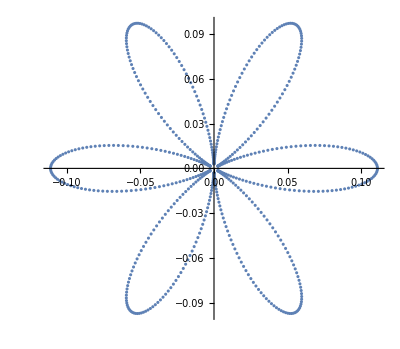

```mathematica
ListPolarPlot[Transpose[{phiList,gapslist}],AspectRatio->Automatic]
```

## Band-Structure

```mathematica
Heff = {{0,Exp[I ϕ] kx + a1, Exp[-I ϕ] ky + a2},{Conjugate[a1]+Exp[-I ϕ]kx,0,Exp[I ϕ]kz + a3},{Exp[I ϕ] ky + Conjugate[a2],Exp[-I ϕ]kz + Conjugate[a3],0}};
a1 = I (Exp[-2 I ϕ]kz)/(2 η ω)A0 (η - r Cos[α]);
a2 = I (Exp[2 I ϕ]kz)/(2 η ω) A0 r Sin[α];
a3 = - I Exp[-2 I ϕ] A0/(2 ω η)( A0 r^2 + (kx - A0)η - r (kx Cos[α] + ky Sin[α]));
```

```mathematica
Energies[k1_,k2_,k3_,phii_,eta_,al_,rr_]:= Sort[Eigenvalues[N[Heff/.{kx->k1,ky->k2,kz->k3,η->eta,ϕ->phii,ω->3,α->al,r->rr,A0->1}]]];
```

```mathematica
(*r=η/Cos[α],α=0,ϕ=0*)
```

```mathematica
Show[Show[Plot3D[{Energies[0,ky,kz,0,2,0,2][[1]],Energies[0,ky,kz,0,2,0,2][[2]],Energies[0,ky,kz,0,2,0,2][[3]]},{ky,-Pi,Pi},{kz,-Pi,Pi},PlotRange->All,Mesh->None,PlotStyle->{Directive[Opacity[0.4],Blue],
Directive[Opacity[0.4],Red],Directive[Opacity[0.4],Green]},RegionFunction->Function[{kx,ky,z},kx^2+ky^2<=2],BoxRatios->Automatic,Axes->True],
Graphics3D[
{
Blue,Line[{{-Sqrt[2],0,0},{Sqrt[2],0,0}}],
Blue, Line[{{0,-Sqrt[2],0},{0,Sqrt[2],0}}],
Red, Line[{{0,0,-1},{0,0,1}}]
}
]

],Frame->True,LabelStyle->Directive[Bold, Black,14]]
```

-Graphics3D-

```mathematica
(*r=η/Cos[α],α=0,ϕ=Pi/6*)
```

```mathematica
Show[Plot3D[{Energies[0,ky,kz,Pi/6,2,0,2][[1]],Energies[0,ky,kz,Pi/6,2,0,2][[2]],Energies[0,ky,kz,Pi/6,2,0,2][[3]]},{ky,-Pi/2,Pi/2},{kz,-Pi/2,Pi/2},PlotRange->All,Mesh->None,PlotStyle->{Directive[Opacity[0.4],Blue],
Directive[Opacity[0.4],Red],Directive[Opacity[0.4],Green]},RegionFunction->Function[{kx,ky,z},kx^2+ky^2<=2],BoxRatios->Automatic,AxesLabel->{"k_y","k_z"}],
Graphics3D[
{
Blue,Line[{{-Sqrt[2],0,0},{Sqrt[2],0,0}}],
Blue, Line[{{0,-Sqrt[2],0},{0,Sqrt[2],0}}],
Red, Line[{{0,0,-1.5},{0,0,1.5}}]
}
]
]
```

-Graphics3D-

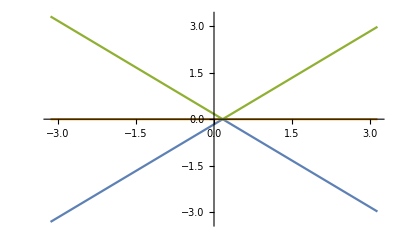

```mathematica
Plot[{Energies[0,0,kz,Pi/6,2,0,2][[1]],Energies[0,0,kz,Pi/6,2,0,2][[2]],Energies[0,0,kz,Pi/6,2,0,2][[3]]},{kz,-Pi,Pi}]
```

```mathematica
(*r=η/Cos[α],α=Pi/4,ϕ=0*)
```

```mathematica
Show[Plot3D[{Energies[0,ky,kz,0,2,Pi/4,2/Cos[Pi/4]][[1]],Energies[0,ky,kz,0,2,Pi/4,2/Cos[Pi/4]][[2]],Energies[0,ky,kz,0,2,Pi/4,2/Cos[Pi/4]][[3]]},{ky,-Pi,Pi},{kz,-Pi,Pi},PlotRange->{All,All,{-2,2}},Mesh->None,PlotStyle->{Directive[Opacity[0.4],Blue],
Directive[Opacity[0.4],Red],Directive[Opacity[0.4],Green]},RegionFunction->Function[{kx,ky,z},kx^2+ky^2<=2],BoxRatios->Automatic,AxesLabel->{Style["k_y",Bold,Black,24],Style["k_z",Bold,Black,24],Style["E",Bold,Black,24]},LabelStyle->Directive[ Black,24]],
Graphics3D[
{
Blue,Line[{{-Sqrt[2],0,0},{Sqrt[2],0,0}}],
Blue, Line[{{0,-Sqrt[2],0},{0,Sqrt[2],0}}],
Red, Line[{{0,0,-1.5},{0,0,1.5}}]
}
]
]
```

-Graphics3D-

```mathematica
Export["/Users/aneekphys/Documents/BCL plots/BCL_eta_2_r_eq_eta_by_cos_alpha_phi_0_alpha_pi_by_4.pdf",%]
```

/Users/aneekphys/Documents/BCL plots/BCL_eta_2_r_eq_eta_by_cos_alpha_phi_0_alpha_pi_by_4.pdf

```mathematica
Export["/Users/aneekphys/Documents/BCL plots/BCL_eta_2_r_eq_eta_by_cos_alpha_phi_pi_by_6_alpha_pi_by_4.pdf",%]
```

/Users/aneekphys/Documents/BCL plots/BCL_eta_2_r_eq_eta_by_cos_alpha_phi_pi_by_6_alpha_pi_by_4.pdf

```mathematica
(*r=η/Cos[α],α=Pi/4,ϕ=Pi/6*)
```

```mathematica
Show[Plot3D[{Energies[0,ky,kz,Pi/6,2,Pi/4,2/Cos[Pi/4]][[1]],Energies[0,ky,kz,Pi/6,2,Pi/4,2/Cos[Pi/4]][[2]],Energies[0,ky,kz,Pi/6,2,Pi/4,2/Cos[Pi/4]][[3]]},{ky,-Pi/2,Pi/2},{kz,-Pi/2,Pi/2},PlotRange->{All,All,{-2,2}},Mesh->None,PlotStyle->{Directive[Opacity[0.4],Blue],
Directive[Opacity[0.4],Red],Directive[Opacity[0.4],Green]},RegionFunction->Function[{kx,ky,z},kx^2+ky^2<=2],BoxRatios->Automatic,AxesLabel->{Style["k_y",Bold,Black,24],Style["k_z",Bold,Black,24],Style["E",Bold,Black,24]},LabelStyle->Directive[ Black,24],MaxRecursion->4],
Graphics3D[
{
Blue,Line[{{-Sqrt[2],0,0},{Sqrt[2],0,0}}],
Blue, Line[{{0,-Sqrt[2],0},{0,Sqrt[2],0}}],
Red, Line[{{0,0,-1.5},{0,0,1.5}}]
}
]
]
```

-Graphics3D-

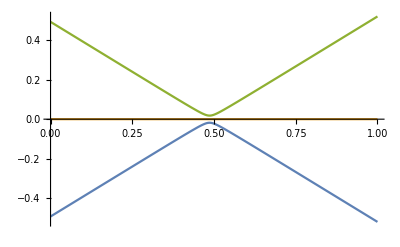

```mathematica
Plot[{Energies[0,0.099,kz,Pi/6,2,Pi/4,2/Cos[Pi/4]][[1]],Energies[0,0.099,kz,Pi/6,2,Pi/4,2/Cos[Pi/4]][[2]],Energies[0,0.099,kz,Pi/6,2,Pi/4,2/Cos[Pi/4]][[3]]},{kz,0,1}]
```

```mathematica
(*α = Pi/2*)
```

```mathematica
(*r=2,ϕ=0*)
```

```mathematica
Show[Plot3D[{Energies[0,ky,kz,0,2,Pi/2,2][[1]],Energies[0,ky,kz,0,2,Pi/2,2][[2]],Energies[0,ky,kz,0,2,Pi/2,2][[3]]},{ky,-Pi,Pi},{kz,-Pi,Pi},PlotRange->All,Mesh->None,PlotStyle->{Directive[Opacity[0.4],Blue],
Directive[Opacity[0.4],Red],Directive[Opacity[0.4],Green]},RegionFunction->Function[{kx,ky,z},kx^2+ky^2<=2],BoxRatios->Automatic,AxesLabel->{"k_y","k_z"},MaxRecursion->4],
Graphics3D[
{
Blue,Line[{{-Sqrt[2],0,0},{Sqrt[2],0,0}}],
Blue, Line[{{0,-Sqrt[2],0},{0,Sqrt[2],0}}],
Red, Line[{{0,0,-1},{0,0,1}}]
}
]
]
```

-Graphics3D-

```mathematica
(*r=2,ϕ=Pi/6*)
```

```mathematica
Show[Plot3D[{Energies[0,ky,kz,Pi/6,2,Pi/2,2][[1]],Energies[0,ky,kz,Pi/6,2,Pi/2,2][[2]],Energies[0,ky,kz,Pi/6,2,Pi/2,2][[3]]},{ky,-Pi,Pi},{kz,-Pi,Pi},PlotRange->All,Mesh->None,PlotStyle->{Directive[Opacity[0.4],Blue],
Directive[Opacity[0.4],Red],Directive[Opacity[0.4],Green]},RegionFunction->Function[{kx,ky,z},kx^2+ky^2<=2],BoxRatios->Automatic,AxesLabel->{"k_y","k_z"},MaxRecursion->4],
Graphics3D[
{
Blue,Line[{{-Sqrt[2],0,0},{Sqrt[2],0,0}}],
Blue, Line[{{0,-Sqrt[2],0},{0,Sqrt[2],0}}],
Red, Line[{{0,0,-1},{0,0,1}}]
}
]
]
```

-Graphics3D-

```mathematica
(*r=√2,ϕ=Pi/6*)
```

```mathematica
Show[Plot3D[{Energies[0,ky,kz,Pi/6,2,Pi/2,Sqrt[2]][[1]],Energies[0,ky,kz,Pi/6,2,Pi/2,Sqrt[2]][[2]],Energies[0,ky,kz,Pi/6,2,Pi/2,Sqrt[2]][[3]]},{ky,-Pi,Pi},{kz,-Pi,Pi},PlotRange->{All,All,{-2,2}},Mesh->None,PlotStyle->{Directive[Opacity[0.4],Blue],
Directive[Opacity[0.4],Red],Directive[Opacity[0.4],Green]},RegionFunction->Function[{kx,ky,z},kx^2+ky^2<=2],BoxRatios->Automatic,AxesLabel->{Style["k_y",Bold,Black,24],Style["k_z",Bold,Black,24],Style["E",Bold,Black,24]},LabelStyle->Directive[ Black,24],MaxRecursion->4],
Graphics3D[
{
Blue,Line[{{-Sqrt[2],0,0},{Sqrt[2],0,0}}],
Blue, Line[{{0,-Sqrt[2],0},{0,Sqrt[2],0}}],
Red, Line[{{0,0,-1},{0,0,1}}]
}
]]
```

-Graphics3D-

```mathematica
Export["/Users/aneekphys/Documents/BCL plots/BCL_eta_2_r_eq_sqrt_2_phi_pi_by_6_alpha_pi_by_2.pdf",%]
```

/Users/aneekphys/Documents/BCL plots/BCL_eta_2_r_eq_sqrt_2_phi_pi_by_6_alpha_pi_by_2.pdf

```mathematica
(*r=√2,ϕ=0*)
Show[Plot3D[{Energies[0,ky,kz,0,2,Pi/2,Sqrt[2]][[1]],Energies[0,ky,kz,0,2,Pi/2,Sqrt[2]][[2]],Energies[0,ky,kz,0,2,Pi/2,Sqrt[2]][[3]]},{ky,-Pi,Pi},{kz,-Pi,Pi},PlotRange->{All,All,{-2,2}},Mesh->None,PlotStyle->{Directive[Opacity[0.4],Blue],
Directive[Opacity[0.4],Red],Directive[Opacity[0.4],Green]},RegionFunction->Function[{kx,ky,z},kx^2+ky^2<=2],BoxRatios->Automatic,AxesLabel->{Style["k_y",Bold,Black,24],Style["k_z",Bold,Black,24],Style["E",Bold,Black,24]},LabelStyle->Directive[ Black,24],MaxRecursion->4],
Graphics3D[
{
Blue,Line[{{-Sqrt[2],0,0},{Sqrt[2],0,0}}],
Blue, Line[{{0,-Sqrt[2],0},{0,Sqrt[2],0}}],
Red, Line[{{0,0,-1},{0,0,1}}]
}
]]
```

-Graphics3D-

```mathematica
Export["/Users/aneekphys/Documents/BCL plots/BCL_eta_2_r_eq_sqrt_2_phi_0_alpha_pi_by_2.pdf",%]
```

/Users/aneekphys/Documents/BCL plots/BCL_eta_2_r_eq_sqrt_2_phi_0_alpha_pi_by_2.pdf

```mathematica
Show[Plot3D[Sin[x y],{x,-3,3},{y,-3,3},PlotStyle->Opacity[0.45],Mesh-> None],Graphics3D[{Red,Line[{{-3,-3,0},{3,3,0}}],Blue,Line[{{-3,3,0},{3,-3,0}}]}]]
```

-Graphics3D-

```mathematica
Solve[56-2 x == 56^(2/3)(0.7(2 x -1))/(4 22),x]
```

{{x→25.132}}